# Matrix test

Solving a system of equations by using matrices
Solve for 3x + 2y = 7 and -6x + 6y = 6

3x + 2y = 7
2y = -3x + 7
y = -3x/2 + 7/2

-6x + 6y = 6
6y = 6x + 6
y = 6x/6 + 6/6
y = x + 1

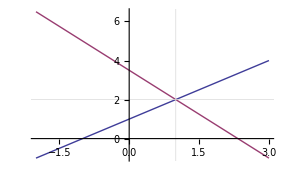

```mathematica
Plot[{x + 1, -3/2x+7/2},  {x, -2, 3}, GridLines->{{1},{ 2}},
GridLinesStyle->LightGray]
```

```mathematica
x=1; y=2;
{3x+2y==7, -6x+6y==6}
```

{True,True}

```mathematica
-6x+6y==6
```

True

```mathematica
6y==6+6x
```

True

```mathematica
6y/6==6/6+6x/6
```

True

```mathematica
1y==1+1x
```

True

```mathematica
y==1+x
```

True

```mathematica
MatrixForm[Inverse[({{1, 0, 1}, {0, 2, 1}, {1, 1, 1}})]]
```

(-1 | -1 | 2
-1 | 0 | 1
2 | 1 | -2)

```mathematica
A={1,2,3}
B={4,5,6}
```

{1,2,3}

{4,5,6}

```mathematica
Dot[A,B]
```

32

```mathematica
Cross[A,B]
```

{-3,6,-3}

```mathematica
Graphics3D[{Arrow[{{0,0,0},A}], Arrow[{{0,0,0},Cross[A,B]}]}]
```

-Graphics3D-

```mathematica
ListPlot3D[{A,{0,0,0},Cross[A, B]}, Mesh->None]
```

-Graphics3D-

```mathematica
sp = SparseArray[RandomInteger[1, {60, 60}]]
```

SparseArray[<1829>,{60,60}]

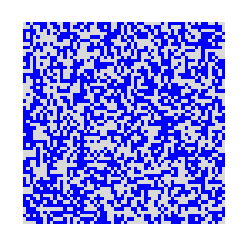

```mathematica
ArrayPlot[sp, ColorRules->{1->Blue,0->LightGray}]
```